```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/olin/fall2016/ThinkBayes2/bayesianLinearRegression

```mathematica
intensityData=Import["intensityData.csv","CSV"]
```

{{23.7391,90.3623,0},{33.942,78.1884,0},{18.3188,67.029,0},{26.2899,75.1449,0},4892,{24.058,86.3043,1},{35.5362,95.942,0},{29.4783,91.3768,0},{27.2464,75.1449,1}}
 |  |  |  |

```mathematica
monthHeightData=Import["monthsHeights.csv","CSV"]
```

{{18,76.1},{19,77.},{20,78.1},{21,78.2},{22,78.8},{23,79.7},{24,79.9},{25,81.1},{26,81.2},{27,81.8},{28,82.8},{29,83.5}}

```mathematica
fittedLine=Import["fittedLineCSV.csv","CSV"]
```

{{18,76.3577},{19,76.9927},{20,77.6276},{21,78.2626},{22,78.8976},{23,79.5325},{24,80.1675},{25,80.8024},{26,81.4374},{27,82.0724},{28,82.7073},{29,83.3423}}

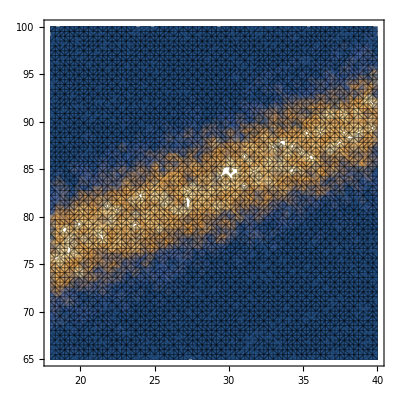

```mathematica
densityPlot=ListDensityPlot[intensityData,Mesh->All]
```

```mathematica
dataPlot=ListPlot[monthHeightData,PlotStyle->Directive[Green,PointSize[.03]]];
fittedLinePlot=ListLinePlot[fittedLine,PlotStyle->Red];
```

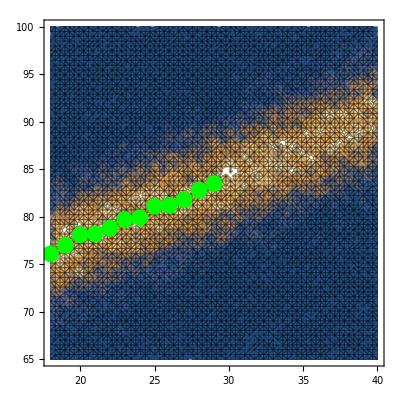

```mathematica
Show[densityPlot,dataPlot,fittedLinePlot]
```